```mathematica
CalculateInOutFormula[g_,in_,out_]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex},
edges=EdgeList[g];
For[pos=1,pos <=Length[edges],pos++,
currentEdge=edges[[pos]];
isInOut=MemberQ[in,currentEdge[[1]]]&&MemberQ[out,currentEdge[[2]]];
If[!isInOut,
isInOut=MemberQ[in,currentEdge[[2]]]&&MemberQ[out,currentEdge[[1]]];
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
If[isInOut,
gContract=GContract[g,currentEdge];
repVertex={currentEdge[[1]]->currentEdge[[2]]};
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
gRemove=EdgeDelete[g,currentEdge];
resContract=CalculateInOutFormula[gContract,DeleteCases[in,currentEdge[[1]]],out];
resRemove=CalculateInOutFormula[gRemove,in,out];
(*Print[currentEdge->{Graph[gRemove,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resRemove,Graph[gContract,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resContract}];*)
result=resRemove-resContract;
Return[result]
];
];
gIn=Subgraph[g,in];
gOut=Subgraph[g,out];
resIn=ChromaticPolynomial[gIn,x];
resOut=If[VertexCount[gOut]==0,1,Fold [Plus,FindFullFormula[gOut]]];
(*Print[{Graph[gIn,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resIn,Graph[gOut,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"], resOut,resIn*resOut}];*)
Return[resIn*resOut]
]
```

```mathematica
MyRewrite[form_]:=Block[{vars=DeleteCases[DeleteDuplicates[ListofVars[form]],x]},
If[vars=={},
Factor[form],
Total[
Table[
v*Factor[Last[CoefficientList[form,v]]],
{v,vars}
]
]
]
]
```

```mathematica
CalculateInOutFormula[g_,in_]:=CalculateInOutFormula[g,in,Select[VertexList[g],!MemberQ[in,#]&]]
```

```mathematica
SymbolToGraph[s_]:=Block[{sets=SymbolToSets[s]},
Symbol["K"<>ToString[Length[sets]]]]
```

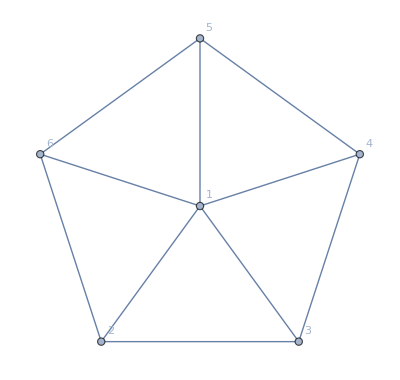

```mathematica
WheelGraph [6,VertexLabels->"Name"]
```

```mathematica
RepChrom=Table[Symbol["K"<>ToString[k]]->ChromaticPolynomial[CompleteGraph[k],x],{k,10}]
```

{K1→x,K2→-x+x^2,K3→2 x-3 x^2+x^3,K4→-6 x+11 x^2-6 x^3+x^4,K5→24 x-50 x^2+35 x^3-10 x^4+x^5,K6→-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6,K7→720 x-1764 x^2+1624 x^3-735 x^4+175 x^5-21 x^6+x^7,K8→-5040 x+13068 x^2-13132 x^3+6769 x^4-1960 x^5+322 x^6-28 x^7+x^8,K9→40320 x-109584 x^2+118124 x^3-67284 x^4+22449 x^5-4536 x^6+546 x^7-36 x^8+x^9,K10→-362880 x+1026576 x^2-1172700 x^3+723680 x^4-269325 x^5+63273 x^6-9450 x^7+870 x^8-45 x^9+x^10}

```mathematica
DeleteCases[VertexList[WheelGraph [4]],{1}]
```

{1,2,3,4}

```mathematica
With[{g=CompleteGraph [3]},
TableForm[
Monitor[
Table[s->MyRewrite[CalculateInOutFormula[g,s]],{s,Subsets[VertexList[g]]}],
s]
]
]
```

{}→v1x2x3
{1}→v2x3 (-2+x)
{2}→v1x3 (-2+x)
{3}→v1x2 (-2+x)
{1,2}→v3 (-2+x) (-1+x)
{1,3}→v2 (-2+x) (-1+x)
{2,3}→v1 (-2+x) (-1+x)
{1,2,3}→(-2+x) (-1+x) x

```mathematica
With[{g=CompleteGraph [6]},
TableForm[
Monitor[
Table[s->Expand[CalculateInOutFormula[g,s]],{s,Subsets[VertexList[g]]}],
s]
]
]
```

{}→v1x2x3x4x5x6
{1}→-5 v2x3x4x5x6+v2x3x4x5x6 x
{2}→-5 v1x3x4x5x6+v1x3x4x5x6 x
{3}→-5 v1x2x4x5x6+v1x2x4x5x6 x
{4}→-5 v1x2x3x5x6+v1x2x3x5x6 x
{5}→-5 v1x2x3x4x6+v1x2x3x4x6 x
{6}→-5 v1x2x3x4x5+v1x2x3x4x5 x
{1,2}→20 v3x4x5x6-9 v3x4x5x6 x+v3x4x5x6 x^2
{1,3}→20 v2x4x5x6-9 v2x4x5x6 x+v2x4x5x6 x^2
{1,4}→20 v2x3x5x6-9 v2x3x5x6 x+v2x3x5x6 x^2
{1,5}→20 v2x3x4x6-9 v2x3x4x6 x+v2x3x4x6 x^2
{1,6}→20 v2x3x4x5-9 v2x3x4x5 x+v2x3x4x5 x^2
{2,3}→20 v1x4x5x6-9 v1x4x5x6 x+v1x4x5x6 x^2
{2,4}→20 v1x3x5x6-9 v1x3x5x6 x+v1x3x5x6 x^2
{2,5}→20 v1x3x4x6-9 v1x3x4x6 x+v1x3x4x6 x^2
{2,6}→20 v1x3x4x5-9 v1x3x4x5 x+v1x3x4x5 x^2
{3,4}→20 v1x2x5x6-9 v1x2x5x6 x+v1x2x5x6 x^2
{3,5}→20 v1x2x4x6-9 v1x2x4x6 x+v1x2x4x6 x^2
{3,6}→20 v1x2x4x5-9 v1x2x4x5 x+v1x2x4x5 x^2
{4,5}→20 v1x2x3x6-9 v1x2x3x6 x+v1x2x3x6 x^2
{4,6}→20 v1x2x3x5-9 v1x2x3x5 x+v1x2x3x5 x^2
{5,6}→20 v1x2x3x4-9 v1x2x3x4 x+v1x2x3x4 x^2
{1,2,3}→-60 v4x5x6+47 v4x5x6 x-12 v4x5x6 x^2+v4x5x6 x^3
{1,2,4}→-60 v3x5x6+47 v3x5x6 x-12 v3x5x6 x^2+v3x5x6 x^3
{1,2,5}→-60 v3x4x6+47 v3x4x6 x-12 v3x4x6 x^2+v3x4x6 x^3
{1,2,6}→-60 v3x4x5+47 v3x4x5 x-12 v3x4x5 x^2+v3x4x5 x^3
{1,3,4}→-60 v2x5x6+47 v2x5x6 x-12 v2x5x6 x^2+v2x5x6 x^3
{1,3,5}→-60 v2x4x6+47 v2x4x6 x-12 v2x4x6 x^2+v2x4x6 x^3
{1,3,6}→-60 v2x4x5+47 v2x4x5 x-12 v2x4x5 x^2+v2x4x5 x^3
{1,4,5}→-60 v2x3x6+47 v2x3x6 x-12 v2x3x6 x^2+v2x3x6 x^3
{1,4,6}→-60 v2x3x5+47 v2x3x5 x-12 v2x3x5 x^2+v2x3x5 x^3
{1,5,6}→-60 v2x3x4+47 v2x3x4 x-12 v2x3x4 x^2+v2x3x4 x^3
{2,3,4}→-60 v1x5x6+47 v1x5x6 x-12 v1x5x6 x^2+v1x5x6 x^3
{2,3,5}→-60 v1x4x6+47 v1x4x6 x-12 v1x4x6 x^2+v1x4x6 x^3
{2,3,6}→-60 v1x4x5+47 v1x4x5 x-12 v1x4x5 x^2+v1x4x5 x^3
{2,4,5}→-60 v1x3x6+47 v1x3x6 x-12 v1x3x6 x^2+v1x3x6 x^3
{2,4,6}→-60 v1x3x5+47 v1x3x5 x-12 v1x3x5 x^2+v1x3x5 x^3
{2,5,6}→-60 v1x3x4+47 v1x3x4 x-12 v1x3x4 x^2+v1x3x4 x^3
{3,4,5}→-60 v1x2x6+47 v1x2x6 x-12 v1x2x6 x^2+v1x2x6 x^3
{3,4,6}→-60 v1x2x5+47 v1x2x5 x-12 v1x2x5 x^2+v1x2x5 x^3
{3,5,6}→-60 v1x2x4+47 v1x2x4 x-12 v1x2x4 x^2+v1x2x4 x^3
{4,5,6}→-60 v1x2x3+47 v1x2x3 x-12 v1x2x3 x^2+v1x2x3 x^3
{1,2,3,4}→120 v5x6-154 v5x6 x+71 v5x6 x^2-14 v5x6 x^3+v5x6 x^4
{1,2,3,5}→120 v4x6-154 v4x6 x+71 v4x6 x^2-14 v4x6 x^3+v4x6 x^4
{1,2,3,6}→120 v4x5-154 v4x5 x+71 v4x5 x^2-14 v4x5 x^3+v4x5 x^4
{1,2,4,5}→120 v3x6-154 v3x6 x+71 v3x6 x^2-14 v3x6 x^3+v3x6 x^4
{1,2,4,6}→120 v3x5-154 v3x5 x+71 v3x5 x^2-14 v3x5 x^3+v3x5 x^4
{1,2,5,6}→120 v3x4-154 v3x4 x+71 v3x4 x^2-14 v3x4 x^3+v3x4 x^4
{1,3,4,5}→120 v2x6-154 v2x6 x+71 v2x6 x^2-14 v2x6 x^3+v2x6 x^4
{1,3,4,6}→120 v2x5-154 v2x5 x+71 v2x5 x^2-14 v2x5 x^3+v2x5 x^4
{1,3,5,6}→120 v2x4-154 v2x4 x+71 v2x4 x^2-14 v2x4 x^3+v2x4 x^4
{1,4,5,6}→120 v2x3-154 v2x3 x+71 v2x3 x^2-14 v2x3 x^3+v2x3 x^4
{2,3,4,5}→120 v1x6-154 v1x6 x+71 v1x6 x^2-14 v1x6 x^3+v1x6 x^4
{2,3,4,6}→120 v1x5-154 v1x5 x+71 v1x5 x^2-14 v1x5 x^3+v1x5 x^4
{2,3,5,6}→120 v1x4-154 v1x4 x+71 v1x4 x^2-14 v1x4 x^3+v1x4 x^4
{2,4,5,6}→120 v1x3-154 v1x3 x+71 v1x3 x^2-14 v1x3 x^3+v1x3 x^4
{3,4,5,6}→120 v1x2-154 v1x2 x+71 v1x2 x^2-14 v1x2 x^3+v1x2 x^4
{1,2,3,4,5}→-120 v6+274 v6 x-225 v6 x^2+85 v6 x^3-15 v6 x^4+v6 x^5
{1,2,3,4,6}→-120 v5+274 v5 x-225 v5 x^2+85 v5 x^3-15 v5 x^4+v5 x^5
{1,2,3,5,6}→-120 v4+274 v4 x-225 v4 x^2+85 v4 x^3-15 v4 x^4+v4 x^5
{1,2,4,5,6}→-120 v3+274 v3 x-225 v3 x^2+85 v3 x^3-15 v3 x^4+v3 x^5
{1,3,4,5,6}→-120 v2+274 v2 x-225 v2 x^2+85 v2 x^3-15 v2 x^4+v2 x^5
{2,3,4,5,6}→-120 v1+274 v1 x-225 v1 x^2+85 v1 x^3-15 v1 x^4+v1 x^5
{1,2,3,4,5,6}→-120 v x+274 v x^2-225 v x^3+85 v x^4-15 v x^5+v x^6

```mathematica
With[{g=CompleteGraph [5]},
TableForm[
Monitor[
Table[s->Expand[CalculateInOutFormula[g,s]],{s,Subsets[VertexList[g]]}],
s]
]
]
```

```mathematica
With[{g=MinimalGraph [4]},
TableForm[
Monitor[
Table[s->Expand[CalculateInOutFormula[g,s]],{s,Subsets[VertexList[g]]}],
s]
]
]
```

{}→v1x2x35x4+v1x2x3x4x5
{1}→-3 v2x35x4-4 v2x3x4x5+v2x35x4 x+v2x3x4x5 x
{2}→-3 v1x35x4-4 v1x3x4x5+v1x35x4 x+v1x3x4x5 x
{3}→-3 v1x2x4x5+v1x2x4x5 x
{4}→-3 v1x2x35-4 v1x2x3x5+v1x2x35 x+v1x2x3x5 x
{5}→-3 v1x2x3x4+v1x2x3x4 x
{1,2}→6 v35x4+12 v3x4x5-5 v35x4 x-7 v3x4x5 x+v35x4 x^2+v3x4x5 x^2
{1,3}→9 v2x4x5-6 v2x4x5 x+v2x4x5 x^2
{1,4}→6 v2x35+12 v2x3x5-5 v2x35 x-7 v2x3x5 x+v2x35 x^2+v2x3x5 x^2
{1,5}→9 v2x3x4-6 v2x3x4 x+v2x3x4 x^2
{2,3}→9 v1x4x5-6 v1x4x5 x+v1x4x5 x^2
{2,4}→6 v1x35+12 v1x3x5-5 v1x35 x-7 v1x3x5 x+v1x35 x^2+v1x3x5 x^2
{2,5}→9 v1x3x4-6 v1x3x4 x+v1x3x4 x^2
{3,4}→9 v1x2x5-6 v1x2x5 x+v1x2x5 x^2
{3,5}→9 v1x2x4-6 v1x2x4 x+v1x2x4 x^2
{4,5}→9 v1x2x3-6 v1x2x3 x+v1x2x3 x^2
{1,2,3}→-18 v4x5+21 v4x5 x-8 v4x5 x^2+v4x5 x^3
{1,2,4}→-6 v35-24 v3x5+11 v35 x+26 v3x5 x-6 v35 x^2-9 v3x5 x^2+v35 x^3+v3x5 x^3
{1,2,5}→-18 v3x4+21 v3x4 x-8 v3x4 x^2+v3x4 x^3
{1,3,4}→-18 v2x5+21 v2x5 x-8 v2x5 x^2+v2x5 x^3
{1,3,5}→-18 v2x4+21 v2x4 x-8 v2x4 x^2+v2x4 x^3
{1,4,5}→-18 v2x3+21 v2x3 x-8 v2x3 x^2+v2x3 x^3
{2,3,4}→-18 v1x5+21 v1x5 x-8 v1x5 x^2+v1x5 x^3
{2,3,5}→-18 v1x4+21 v1x4 x-8 v1x4 x^2+v1x4 x^3
{2,4,5}→-18 v1x3+21 v1x3 x-8 v1x3 x^2+v1x3 x^3
{3,4,5}→-18 v1x2+21 v1x2 x-8 v1x2 x^2+v1x2 x^3
{1,2,3,4}→18 v5-39 v5 x+29 v5 x^2-9 v5 x^3+v5 x^4
{1,2,3,5}→18 v4-39 v4 x+29 v4 x^2-9 v4 x^3+v4 x^4
{1,2,4,5}→18 v3-39 v3 x+29 v3 x^2-9 v3 x^3+v3 x^4
{1,3,4,5}→18 v2-39 v2 x+29 v2 x^2-9 v2 x^3+v2 x^4
{2,3,4,5}→18 v1-39 v1 x+29 v1 x^2-9 v1 x^3+v1 x^4
{1,2,3,4,5}→18 v x-39 v x^2+29 v x^3-9 v x^4+v x^5

```mathematica
Expand[CalculateInOutFormula[WheelGraph [4],{1}]]
```

-3 v2x3x4+v2x3x4 x

```mathematica
Expand[CalculateInOutFormula[WheelGraph [4],{1},{2,3,4}]]
```

-3 v2x3x4+v2x3x4 x

```mathematica
Expand[CalculateInOutFormula[WheelGraph [5],{1},{2,3,4,5}]]
```

-2 v24x35-3 v24x3x5-3 v2x35x4-4 v2x3x4x5+v24x35 x+v24x3x5 x+v2x35x4 x+v2x3x4x5 x

```mathematica
Reduce[Collect[Expand[CalculateInOutFormula[WheelGraph [6],{1},{2,3,4,5,6}]],x]==0]
```

(x==3&&v24x3x5x6==-v25x3x4x6-v2x35x4x6-v2x36x4x5-v2x3x46x5-2 v2x3x4x5x6)||(-3+x≠0&&v24x35x6==1/(-3+x)(3 v24x36x5+4 v24x3x5x6+3 v25x36x4+3 v25x3x46+4 v25x3x4x6+3 v2x35x46+4 v2x35x4x6+4 v2x36x4x5+4 v2x3x46x5+5 v2x3x4x5x6-v24x36x5 x-v24x3x5x6 x-v25x36x4 x-v25x3x46 x-v25x3x4x6 x-v2x35x46 x-v2x35x4x6 x-v2x36x4x5 x-v2x3x46x5 x-v2x3x4x5x6 x))

```mathematica
Expand[-2 K2-6 K3-4 K4+K2 x+2 K3 x+K4 x/.RepChrom]
```

14 x-31 x^2+24 x^3-8 x^4+x^5

```mathematica
ChromaticPolynomial[WheelGraph[5],x]
```

14 x-31 x^2+24 x^3-8 x^4+x^5

```mathematica
Expand[K3 x/.RepChrom]
```

2 x^2-3 x^3+x^4

```mathematica
Expand[-3 K2/.RepChrom]
```

3 x-3 x^2

```mathematica
Expand[-5 (-x+x^2)-15 (2 x-3 x^2+x^3)-5 (-6 x+11 x^2-6 x^3+x^4)+x (24 x-50 x^2+35 x^3-10 x^4+x^5+5 (2 x-3 x^2+x^3)+5 (-6 x+11 x^2-6 x^3+x^4))]
```

5 x-11 x^2+5 x^3+5 x^4-5 x^5+x^6

```mathematica
ChromaticPolynomial[WheelGraph[4],x]
```

-6 x+11 x^2-6 x^3+x^4

## Other way of calculating out

```mathematica
CalculateInOutFormula2[g_,in_,out_]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex},
edges=EdgeList[g];
For[pos=1,pos <=Length[edges],pos++,
currentEdge=edges[[pos]];
isInOut=MemberQ[in,currentEdge[[1]]]&&MemberQ[out,currentEdge[[2]]];
If[!isInOut,
isInOut=MemberQ[in,currentEdge[[2]]]&&MemberQ[out,currentEdge[[1]]];
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
If[isInOut,
gContract=GContract[g,currentEdge];
repVertex={currentEdge[[1]]->currentEdge[[2]]};
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
gRemove=EdgeDelete[g,currentEdge];
resContract=CalculateInOutFormula2[gContract,DeleteCases[in,currentEdge[[1]]],out];
resRemove=CalculateInOutFormula2[gRemove,in,out];
(*Print[currentEdge->{Graph[gRemove,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resRemove,Graph[gContract,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resContract}];*)
result=resRemove-resContract;
Return[result]
];
];
gIn=Subgraph[g,in];
gOut=Subgraph[g,out];
resIn=ChromaticPolynomial[gIn,x];
resOut=Graph[gOut,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"];
(*Print[{Graph[gIn,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resIn,Graph[gOut,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"], resOut,resIn*resOut}];*)
Return[resIn*resOut]
]
```

```mathematica
CalculateInOutFormula2[g_,in_]:=CalculateInOutFormula2[g,in,Select[VertexList[g],!MemberQ[in,#]&]]
```

```mathematica
Simplify[Expand[CalculateInOutFormula[WheelGraph [6],{1},{2,3,4,5,6}]]]
```

```mathematica
Simplify[Expand[CalculateInOutFormula2[WheelGraph [6],{1},{2,3,4,5,6}]]]
```

--Graphics---Graphics---Graphics---Graphics---Graphics-+-Graphics- x

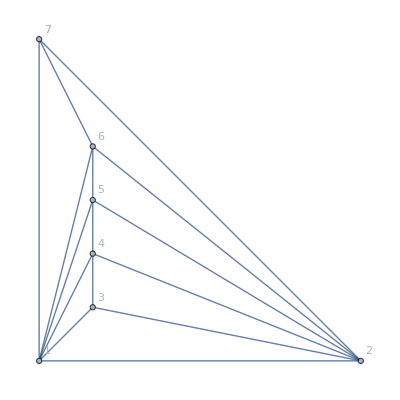

```mathematica
MinimalGraph[6]
```

```mathematica
Simplify[Expand[CalculateInOutFormula2[MinimalGraph[4],{3,4},{1,2,5}]]]
```

3 -Graphics-+-Graphics-+-Graphics- (3-2 x)--Graphics- (-2+x)--Graphics- x-2 -Graphics- x+-Graphics- x^2

```mathematica
Simplify[Expand[CalculateInOutFormula[MinimalGraph[6],{3,4,5,6},{1,2,7}]]]
```

v1x2x7 (-3+x)^4

```mathematica
Simplify[Expand[CalculateInOutFormula[MinimalGraph[6],{7,4,5,6},{1,2,3}]]]
```

v1x2x3 (-3+x)^4

```mathematica
Simplify[Expand[CalculateInOutFormula[MinimalGraph[6],{7,4,5,6},{1,2,3}]]]
```

```mathematica
Simplify[Expand[CalculateInOutFormula[MinimalGraph[6],{1,2,4,6},{3,5,7}]]]
```

(-3+x) (v357 (-6+11 x-6 x^2+x^3)+(-4+x) (6 v3x57+16 v3x5x7-5 v3x57 x-8 v3x5x7 x+v3x57 x^2+v3x5x7 x^2+v37x5 (8-6 x+x^2)+v35x7 (6-5 x+x^2)))

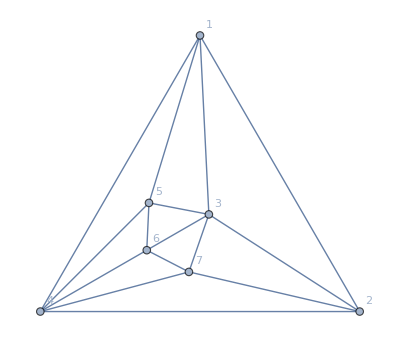

```mathematica
Graph[JacobsThalGraph[3],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
Simplify[Expand[CalculateInOutFormula[JacobsThalGraph[3],{3,5,6,7},{1,2,4}]]]//Factor
```

v1x2x4 (-3+x) (-35+30 x-9 x^2+x^3)

```mathematica
Collect[Expand[CalculateInOutFormula[JacobsThalGraph[3],{1,3,6,7},{5,2,4}]],x]
```

60 v25x4+135 v2x4x5+(-86 v25x4-153 v2x4x5) x+(46 v25x4+66 v2x4x5) x^2+(-11 v25x4-13 v2x4x5) x^3+(v25x4+v2x4x5) x^4

```mathematica
Collect[Expand[CalculateInOutFormula[JacobsThalGraph[3],{2,3,5,6},{1,4,7}]],x]
```

60 v17x4+135 v1x4x7+(-86 v17x4-153 v1x4x7) x+(46 v17x4+66 v1x4x7) x^2+(-11 v17x4-13 v1x4x7) x^3+(v17x4+v1x4x7) x^4

```mathematica
Simplify[Expand[CalculateInOutFormula[JacobsThalGraph[3],{1,5,6,4},{2,3,7}]]]//Factor
```

v2x3x7 (-3+x) (-35+30 x-9 x^2+x^3)

```mathematica
Simplify[Expand[CalculateInOutFormula[JacobsThalGraph[3],{1,3,5,6},{2,4,7}]]]//Factor
```

v2x4x7 (-3+x) (-35+30 x-9 x^2+x^3)

```mathematica
Simplify[Expand[CalculateInOutFormula[JacobsThalGraph[3],{1,2,4,7},{3,5,6}]]]//Factor
```

v3x5x6 (-3+x) (-35+30 x-9 x^2+x^3)

```mathematica
Simplify[Expand[CalculateInOutFormula[JacobsThalGraph[3],{1,3,5},{2,4,6,7}]]]//Factor
```

(-3+x) (10 v26x4x7+15 v2x4x6x7-6 v26x4x7 x-7 v2x4x6x7 x+v26x4x7 x^2+v2x4x6x7 x^2)

```mathematica
ChromaticPolynomial[JacobsThalGraph[3],x]
```

210 x-565 x^2+594 x^3-320 x^4+95 x^5-15 x^6+x^7

```mathematica
CompleteBaseCoeff[105-125 x+57 x^2-12 x^3+x^4]
```

{105,-79,28,-6,1}

```mathematica
Collect[Expand[CalculateInOutFormula[WheelGraph[6],{1},{2,3,4,5,6}]],x]
```

-3 v24x35x6-3 v24x36x5-4 v24x3x5x6-3 v25x36x4-3 v25x3x46-4 v25x3x4x6-3 v2x35x46-4 v2x35x4x6-4 v2x36x4x5-4 v2x3x46x5-5 v2x3x4x5x6+(v24x35x6+v24x36x5+v24x3x5x6+v25x36x4+v25x3x46+v25x3x4x6+v2x35x46+v2x35x4x6+v2x36x4x5+v2x3x46x5+v2x3x4x5x6) x

```mathematica
Collect[Expand[CalculateInOutFormula[WheelGraph[6],{2},{1,3,4,5,6}]],x]
```

-3 v1x35x46-3 v1x35x4x6-2 v1x36x4x5-3 v1x3x46x5-3 v1x3x4x5x6+(v1x35x46+v1x35x4x6+v1x36x4x5+v1x3x46x5+v1x3x4x5x6) x

```mathematica
Collect[Expand[CalculateInOutFormula[WheelGraph[6],{1,2},{3,4,5,6}]],x]
```

6 v35x46+9 v35x4x6+6 v36x4x5+9 v3x46x5+12 v3x4x5x6+(-5 v35x46-6 v35x4x6-5 v36x4x5-6 v3x46x5-7 v3x4x5x6) x+(v35x46+v35x4x6+v36x4x5+v3x46x5+v3x4x5x6) x^2

```mathematica
Collect[Expand[CalculateInOutFormula[WheelGraph[6],{1,2,3},{4,5,6}]],x]
```

-12 v46x5-21 v4x5x6+(16 v46x5+22 v4x5x6) x+(-7 v46x5-8 v4x5x6) x^2+(v46x5+v4x5x6) x^3

```mathematica
Collect[Expand[CalculateInOutFormula[WheelGraph[6],{1,2,3,4},{5,6}]],x]
```

30 v5x6-49 v5x6 x+31 v5x6 x^2-9 v5x6 x^3+v5x6 x^4

```mathematica
Collect[Expand[CalculateInOutFormula[WheelGraph[6],{1,2,3,4,5},{6}]],x]
```

-30 v6+79 v6 x-80 v6 x^2+40 v6 x^3-10 v6 x^4+v6 x^5

```mathematica
ChromaticPolynomial[WheelGraph[6],x]
```

-30 x+79 x^2-80 x^3+40 x^4-10 x^5+x^6

```mathematica
Eliminate[-30 v6+79 v6 x-80 v6 x^2+40 v6 x^3-10 v6 x^4+v6 x^5==-30 v6+79 v6 x-80 v6 x^2+40 v6 x^3-10 v6 x^4+v6 x^5,x]
```

True

```mathematica
Solve[30 v5x6-49 v5x6 x+31 v5x6 x^2-9 v5x6 x^3+v5x6 x^4==-30 v6+79 v6 x-80 v6 x^2+40 v6 x^3-10 v6 x^4+v6 x^5,x]
```

{{x→2},{x→2-ⅈ},{x→2+ⅈ},{x→3},{x→(v5x6+v6)/v6}}

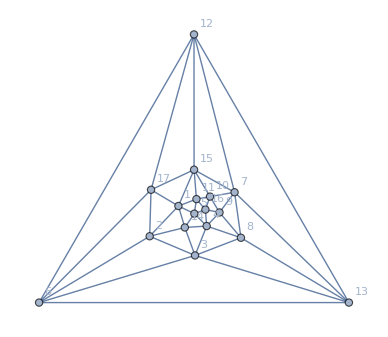

```mathematica
plantri8
```

```mathematica
2^7
```

128

## Calculating some more graphs

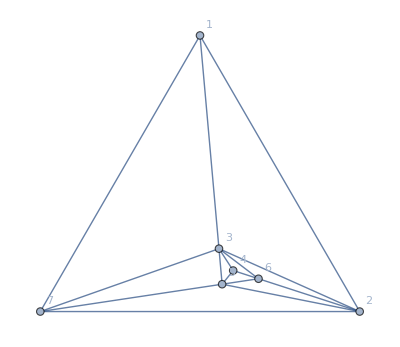
-Graphics-
{}→v14x2x3x5x67+v14x2x3x5x6x7+v15x24x3x67+v15x24x3x6x7+v15x2x3x47x6+v15x2x3x4x67+v15x2x3x4x6x7+v16x24x3x5x7+v16x2x3x47x5+v16x2x3x4x5x7+v1x24x3x5x67+v1x24x3x5x6x7+v1x2x3x47x5x6+v1x2x3x4x5x67+v1x2x3x4x5x6x7
{1}→v24x3x5x67 (-3+x)+v24x3x5x6x7 (-3+x)+v2x3x47x5x6 (-3+x)+v2x3x4x5x67 (-3+x)+v2x3x4x5x6x7 (-3+x)
{2}→v14x3x5x6x7 (-5+x)+v1x3x47x5x6 (-5+x)+v1x3x4x5x6x7 (-5+x)+v14x3x5x67 (-4+x)+v15x3x47x6 (-4+x)+v15x3x4x6x7 (-4+x)+v16x3x47x5 (-4+x)+v16x3x4x5x7 (-4+x)+v1x3x4x5x67 (-4+x)+v15x3x4x67 (-3+x)
{3}→v1x2x4x5x6x7 (-6+x)+v14x2x5x6x7 (-5+x)+v15x2x4x6x7 (-5+x)+v16x2x4x5x7 (-5+x)+v1x24x5x6x7 (-5+x)+v1x2x47x5x6 (-5+x)+v1x2x4x5x67 (-5+x)+v14x2x5x67 (-4+x)+v15x24x6x7 (-4+x)+v15x2x47x6 (-4+x)+v15x2x4x67 (-4+x)+v16x24x5x7 (-4+x)+v16x2x47x5 (-4+x)+v1x24x5x67 (-4+x)+v15x24x67 (-3+x)
{7}→v14x2x3x5x6 (-4+x)+v16x24x3x5 (-4+x)+v16x2x3x4x5 (-4+x)+v1x24x3x5x6 (-4+x)+v1x2x3x4x5x6 (-4+x)+v15x24x3x6 (-3+x)+v15x2x3x4x6 (-3+x)
{5}→v14x2x3x6x7 (-5+x)+v16x2x3x4x7 (-5+x)+v1x2x3x4x6x7 (-5+x)+v14x2x3x67 (-4+x)+v16x24x3x7 (-4+x)+v16x2x3x47 (-4+x)+v1x24x3x6x7 (-4+x)+v1x2x3x47x6 (-4+x)+v1x2x3x4x67 (-4+x)+v1x24x3x67 (-3+x)
{6}→v14x2x3x5x7 (-4+x)+v15x2x3x47 (-4+x)+v15x2x3x4x7 (-4+x)+v1x2x3x47x5 (-4+x)+v1x2x3x4x5x7 (-4+x)+v15x24x3x7 (-3+x)+v1x24x3x5x7 (-3+x)
{4}→v15x2x3x67 (-3+x)+v15x2x3x6x7 (-3+x)+v16x2x3x5x7 (-3+x)+v1x2x3x5x67 (-3+x)+v1x2x3x5x6x7 (-3+x)
{1,2}→v3x47x5x6 (-4+x) (-3+x)+v3x4x5x6x7 (-4+x) (-3+x)+v3x4x5x67 (-3+x)^2
{1,3}→v2x4x5x6x7 (-5+x) (-3+x)+v24x5x6x7 (-4+x) (-3+x)+v2x47x5x6 (-4+x) (-3+x)+v2x4x5x67 (-4+x) (-3+x)+v24x5x67 (-3+x)^2
{1,7}→v24x3x5x6 (-3+x)^2+v2x3x4x5x6 (-3+x)^2
{1,5}→v2x3x4x6x7 (-5+x) (-3+x)+v24x3x6x7 (-4+x) (-3+x)+v2x3x47x6 (-4+x) (-3+x)+v2x3x4x67 (-4+x) (-3+x)+v24x3x67 (-3+x)^2
{1,6}→v2x3x47x5 (-4+x) (-3+x)+v2x3x4x5x7 (-4+x) (-3+x)+v24x3x5x7 (-3+x)^2
{1,4}→v2x3x5x67 (-3+x)^2+v2x3x5x6x7 (-3+x)^2
{2,3}→v1x4x5x6x7 (-5+x)^2+v14x5x6x7 (-5+x) (-4+x)+v1x47x5x6 (-5+x) (-4+x)+v15x4x6x7 (-4+x)^2+v16x4x5x7 (-4+x)^2+v1x4x5x67 (-4+x)^2+v14x5x67 (-4+x) (-3+x)+v15x47x6 (-4+x) (-3+x)+v16x47x5 (-4+x) (-3+x)+v15x4x67 (-3+x)^2
{2,7}→v14x3x5x6 (-4+x)^2+v1x3x4x5x6 (-4+x)^2+v16x3x4x5 (-4+x) (-3+x)+v15x3x4x6 (-3+x)^2
{2,5}→v14x3x6x7 (-5+x) (-4+x)+v16x3x4x7 (-4+x)^2+v1x3x47x6 (-4+x)^2+v14x3x67 (-4+x) (-3+x)+v16x3x47 (-4+x) (-3+x)+v1x3x4x6x7 (21-9 x+x^2)+v1x3x4x67 (13-7 x+x^2)
{2,6}→v14x3x5x7 (-4+x)^2+v1x3x47x5 (-4+x)^2+v15x3x47 (-4+x) (-3+x)+v1x3x4x5x7 (17-8 x+x^2)+v15x3x4x7 (13-7 x+x^2)
{2,4}→v1x3x5x6x7 (-5+x) (-3+x)+v15x3x6x7 (-4+x) (-3+x)+v16x3x5x7 (-4+x) (-3+x)+v1x3x5x67 (-4+x) (-3+x)+v15x3x67 (-3+x)^2
{3,7}→v1x2x4x5x6 (-5+x) (-4+x)+v14x2x5x6 (-4+x)^2+v16x2x4x5 (-4+x)^2+v1x24x5x6 (-4+x)^2+v15x2x4x6 (-4+x) (-3+x)+v16x24x5 (-4+x) (-3+x)+v15x24x6 (-3+x)^2
{3,5}→v1x2x4x6x7 (-5+x)^2+v14x2x6x7 (-5+x) (-4+x)+v16x2x4x7 (-5+x) (-4+x)+v1x24x6x7 (-4+x)^2+v1x2x47x6 (-4+x)^2+v1x2x4x67 (-4+x)^2+v14x2x67 (-4+x) (-3+x)+v16x24x7 (-4+x) (-3+x)+v16x2x47 (-4+x) (-3+x)+v1x24x67 (-3+x)^2
{3,6}→v1x2x4x5x7 (-5+x) (-4+x)+v14x2x5x7 (-4+x)^2+v15x2x4x7 (-4+x)^2+v1x2x47x5 (-4+x)^2+v15x2x47 (-4+x) (-3+x)+v1x24x5x7 (-4+x) (-3+x)+v15x24x7 (-3+x)^2
{3,4}→v1x2x5x6x7 (-5+x) (-3+x)+v15x2x6x7 (-4+x) (-3+x)+v16x2x5x7 (-4+x) (-3+x)+v1x2x5x67 (-4+x) (-3+x)+v15x2x67 (-3+x)^2
{7,5}→v14x2x3x6 (-4+x)^2+v16x2x3x4 (-4+x)^2+v16x24x3 (-4+x) (-3+x)+v1x2x3x4x6 (17-8 x+x^2)+v1x24x3x6 (13-7 x+x^2)
{7,6}→v14x2x3x5 (-4+x)^2+v1x2x3x4x5 (-4+x)^2+v15x2x3x4 (-4+x) (-3+x)+v1x24x3x5 (-4+x) (-3+x)+v15x24x3 (-3+x)^2
{7,4}→v16x2x3x5 (-4+x) (-3+x)+v1x2x3x5x6 (-4+x) (-3+x)+v15x2x3x6 (-3+x)^2
{5,6}→v14x2x3x7 (-4+x)^2+v1x2x3x4x7 (-4+x)^2+v1x2x3x47 (-4+x) (-3+x)+v1x24x3x7 (-3+x)^2
{5,4}→v16x2x3x7 (-4+x) (-3+x)+v1x2x3x6x7 (-4+x) (-3+x)+v1x2x3x67 (-3+x)^2
{6,4}→v15x2x3x7 (-3+x)^2+v1x2x3x5x7 (-3+x)^2
{1,2,3}→v4x5x6x7 (-4+x)^2 (-3+x)+v47x5x6 (-4+x) (-3+x)^2+v4x5x67 (-3+x)^3
{1,2,7}→v3x4x5x6 (-3+x)^3
{1,2,5}→v3x4x6x7 (-4+x)^2 (-3+x)+v3x47x6 (-4+x) (-3+x)^2+v3x4x67 (-3+x)^3
{1,2,6}→v3x47x5 (-4+x) (-3+x)^2+v3x4x5x7 (-3+x) (13-7 x+x^2)
{1,2,4}→v3x5x6x7 (-4+x) (-3+x)^2+v3x5x67 (-3+x)^3
{1,3,7}→v2x4x5x6 (-4+x) (-3+x)^2+v24x5x6 (-3+x)^3
{1,3,5}→v2x4x6x7 (-5+x) (-4+x) (-3+x)+v24x6x7 (-4+x) (-3+x)^2+v2x47x6 (-4+x) (-3+x)^2+v2x4x67 (-4+x) (-3+x)^2+v24x67 (-3+x)^2 (-2+x)
{1,3,6}→v2x4x5x7 (-4+x)^2 (-3+x)+v2x47x5 (-4+x) (-3+x)^2+v24x5x7 (-3+x)^3
{1,3,4}→v2x5x6x7 (-4+x) (-3+x)^2+v2x5x67 (-3+x)^3
{1,7,5}→v2x3x4x6 (-4+x) (-3+x)^2+v24x3x6 (-3+x)^3
{1,7,6}→v2x3x4x5 (-4+x) (-3+x)^2+v24x3x5 (-3+x)^3
{1,7,4}→v2x3x5x6 (-3+x)^3
{1,5,6}→v2x3x4x7 (-4+x)^2 (-3+x)+v2x3x47 (-4+x) (-3+x)^2+v24x3x7 (-3+x)^3
{1,5,4}→v2x3x6x7 (-4+x) (-3+x)^2+v2x3x67 (-3+x)^3
{1,6,4}→v2x3x5x7 (-3+x)^3
{2,3,7}→v1x4x5x6 (-4+x)^3+v14x5x6 (-4+x)^2 (-3+x)+v16x4x5 (-4+x) (-3+x)^2+v15x4x6 (-3+x)^3
{2,3,5}→v14x6x7 (-5+x) (-4+x) (-3+x)+v16x4x7 (-4+x)^2 (-3+x)+v1x47x6 (-4+x)^2 (-3+x)+v14x67 (-4+x) (-3+x) (-2+x)+v16x47 (-4+x) (-3+x) (-2+x)+v1x4x6x7 (-4+x) (21-9 x+x^2)+v1x4x67 (-3+x) (13-7 x+x^2)
{2,3,6}→v14x5x7 (-4+x)^2 (-3+x)+v1x47x5 (-4+x)^2 (-3+x)+v15x47 (-4+x) (-3+x) (-2+x)+v1x4x5x7 (-4+x) (17-8 x+x^2)+v15x4x7 (-3+x) (13-7 x+x^2)
{2,3,4}→v1x5x6x7 (-5+x) (-4+x) (-3+x)+v15x6x7 (-4+x) (-3+x)^2+v16x5x7 (-4+x) (-3+x)^2+v1x5x67 (-4+x) (-3+x)^2+v15x67 (-3+x)^2 (-2+x)
{2,7,5}→v14x3x6 (-4+x)^2 (-3+x)+v16x3x4 (-4+x) (-3+x)^2+v1x3x4x6 (-55+42 x-11 x^2+x^3)
{2,7,6}→v14x3x5 (-4+x)^2 (-3+x)+v15x3x4 (-3+x)^3+v1x3x4x5 (-4+x) (13-7 x+x^2)
{2,7,4}→v1x3x5x6 (-4+x)^2 (-3+x)+v16x3x5 (-4+x) (-3+x)^2+v15x3x6 (-3+x)^3
{2,5,6}→v14x3x7 (-4+x)^2 (-3+x)+v1x3x47 (-4+x) (-3+x)^2+v1x3x4x7 (-55+42 x-11 x^2+x^3)
{2,5,4}→v1x3x6x7 (-4+x)^2 (-3+x)+v16x3x7 (-4+x) (-3+x)^2+v1x3x67 (-3+x)^3
{2,6,4}→v1x3x5x7 (-4+x) (-3+x)^2+v15x3x7 (-3+x)^3
{3,7,5}→v14x2x6 (-4+x)^2 (-3+x)+v16x2x4 (-4+x)^2 (-3+x)+v16x24 (-4+x) (-3+x) (-2+x)+v1x2x4x6 (-4+x) (17-8 x+x^2)+v1x24x6 (-3+x) (13-7 x+x^2)
{3,7,6}→v1x2x4x5 (-4+x)^3+v14x2x5 (-4+x)^2 (-3+x)+v15x2x4 (-4+x) (-3+x)^2+v1x24x5 (-4+x) (-3+x)^2+v15x24 (-3+x)^2 (-2+x)
{3,7,4}→v1x2x5x6 (-4+x)^2 (-3+x)+v16x2x5 (-4+x) (-3+x)^2+v15x2x6 (-3+x)^3
{3,5,6}→v1x2x4x7 (-4+x)^3+v14x2x7 (-4+x)^2 (-3+x)+v1x2x47 (-4+x) (-3+x)^2+v1x24x7 (-3+x)^3
{3,5,4}→v1x2x6x7 (-4+x)^2 (-3+x)+v16x2x7 (-4+x) (-3+x)^2+v1x2x67 (-3+x)^3
{3,6,4}→v1x2x5x7 (-4+x) (-3+x)^2+v15x2x7 (-3+x)^3
{7,5,6}→v14x2x3 (-4+x)^2 (-3+x)+v1x24x3 (-3+x)^3+v1x2x3x4 (-4+x) (13-7 x+x^2)
{7,5,4}→v16x2x3 (-4+x) (-3+x)^2+v1x2x3x6 (-3+x) (13-7 x+x^2)
{7,6,4}→v1x2x3x5 (-4+x) (-3+x)^2+v15x2x3 (-3+x)^3
{5,6,4}→v1x2x3x7 (-3+x)^3
{1,2,3,7}→v4x5x6 (-3+x)^4
{1,2,3,5}→v4x6x7 (-4+x)^2 (-3+x)^2+v47x6 (-4+x) (-3+x)^2 (-2+x)+v4x67 (-3+x)^3 (-2+x)
{1,2,3,6}→v47x5 (-4+x) (-3+x)^2 (-2+x)+v4x5x7 (-3+x)^2 (13-7 x+x^2)
{1,2,3,4}→v5x6x7 (-4+x) (-3+x)^3+v5x67 (-3+x)^3 (-2+x)
{1,2,7,5}→v3x4x6 (-3+x)^4
{1,2,7,6}→v3x4x5 (-3+x)^4
{1,2,7,4}→v3x5x6 (-3+x)^4
{1,2,5,6}→v3x47 (-4+x) (-3+x)^2 (-2+x)+v3x4x7 (-3+x)^2 (13-7 x+x^2)
{1,2,5,4}→v3x6x7 (-4+x) (-3+x)^3+v3x67 (-3+x)^3 (-2+x)
{1,2,6,4}→v3x5x7 (-3+x)^4
{1,3,7,5}→v2x4x6 (-4+x) (-3+x)^3+v24x6 (-3+x)^3 (-2+x)
{1,3,7,6}→v2x4x5 (-4+x) (-3+x)^3+v24x5 (-3+x)^3 (-2+x)
{1,3,7,4}→v2x5x6 (-3+x)^4
{1,3,5,6}→v2x4x7 (-4+x)^2 (-3+x)^2+v2x47 (-4+x) (-3+x)^2 (-2+x)+v24x7 (-3+x)^3 (-2+x)
{1,3,5,4}→v2x6x7 (-4+x) (-3+x)^3+v2x67 (-3+x)^3 (-2+x)
{1,3,6,4}→v2x5x7 (-3+x)^4
{1,7,5,6}→v2x3x4 (-4+x) (-3+x)^3+v24x3 (-3+x)^3 (-2+x)
{1,7,5,4}→v2x3x6 (-3+x)^4
{1,7,6,4}→v2x3x5 (-3+x)^4
{1,5,6,4}→v2x3x7 (-3+x)^4
{2,3,7,5}→v14x6 (-4+x)^2 (-3+x) (-2+x)+v16x4 (-4+x) (-3+x)^2 (-2+x)+v1x4x6 (-3+x) (-55+42 x-11 x^2+x^3)
{2,3,7,6}→v14x5 (-4+x)^2 (-3+x) (-2+x)+v15x4 (-3+x)^3 (-2+x)+v1x4x5 (-4+x) (-3+x) (13-7 x+x^2)
{2,3,7,4}→v1x5x6 (-4+x)^2 (-3+x)^2+v16x5 (-4+x) (-3+x)^2 (-2+x)+v15x6 (-3+x)^3 (-2+x)
{2,3,5,6}→v14x7 (-4+x)^2 (-3+x) (-2+x)+v1x47 (-4+x) (-3+x)^2 (-2+x)+v1x4x7 (-3+x) (-55+42 x-11 x^2+x^3)
{2,3,5,4}→v1x6x7 (-4+x)^2 (-3+x)^2+v16x7 (-4+x) (-3+x)^2 (-2+x)+v1x67 (-3+x)^3 (-2+x)
{2,3,6,4}→v1x5x7 (-4+x) (-3+x)^3+v15x7 (-3+x)^3 (-2+x)
{2,7,5,6}→v14x3 (-4+x)^2 (-3+x) (-2+x)+v1x3x4 (-3+x) (-43+35 x-10 x^2+x^3)
{2,7,5,4}→v16x3 (-4+x) (-3+x)^2 (-2+x)+v1x3x6 (-3+x)^2 (13-7 x+x^2)
{2,7,6,4}→v1x3x5 (-4+x) (-3+x)^3+v15x3 (-3+x)^3 (-2+x)
{2,5,6,4}→v1x3x7 (-3+x)^4
{3,7,5,6}→v14x2 (-4+x)^2 (-3+x) (-2+x)+v1x24 (-3+x)^3 (-2+x)+v1x2x4 (-4+x) (-3+x) (13-7 x+x^2)
{3,7,5,4}→v16x2 (-4+x) (-3+x)^2 (-2+x)+v1x2x6 (-3+x)^2 (13-7 x+x^2)
{3,7,6,4}→v1x2x5 (-4+x) (-3+x)^3+v15x2 (-3+x)^3 (-2+x)
{3,5,6,4}→v1x2x7 (-3+x)^4
{7,5,6,4}→v1x2x3 (-3+x)^4
{1,2,3,7,5}→v4x6 (-3+x)^4 (-2+x)
{1,2,3,7,6}→v4x5 (-3+x)^4 (-2+x)
{1,2,3,7,4}→v5x6 (-3+x)^4 (-2+x)
{1,2,3,5,6}→v47 (-4+x) (-3+x)^2 (-2+x) (-1+x)+v4x7 (-3+x)^2 (-2+x) (13-7 x+x^2)
{1,2,3,5,4}→v6x7 (-4+x) (-3+x)^3 (-2+x)+v67 (-3+x)^3 (-2+x) (-1+x)
{1,2,3,6,4}→v5x7 (-3+x)^4 (-2+x)
{1,2,7,5,6}→v3x4 (-3+x)^4 (-2+x)
{1,2,7,5,4}→v3x6 (-3+x)^4 (-2+x)
{1,2,7,6,4}→v3x5 (-3+x)^4 (-2+x)
{1,2,5,6,4}→v3x7 (-3+x)^4 (-2+x)
{1,3,7,5,6}→v2x4 (-4+x) (-3+x)^3 (-2+x)+v24 (-3+x)^3 (-2+x) (-1+x)
{1,3,7,5,4}→v2x6 (-3+x)^4 (-2+x)
{1,3,7,6,4}→v2x5 (-3+x)^4 (-2+x)
{1,3,5,6,4}→v2x7 (-3+x)^4 (-2+x)
{1,7,5,6,4}→v2x3 (-3+x)^4 (-2+x)
{2,3,7,5,6}→v14 (-4+x)^2 (-3+x) (-2+x) (-1+x)+v1x4 (-3+x) (-2+x) (-43+35 x-10 x^2+x^3)
{2,3,7,5,4}→v16 (-4+x) (-3+x)^2 (-2+x) (-1+x)+v1x6 (-3+x)^2 (-2+x) (13-7 x+x^2)
{2,3,7,6,4}→v1x5 (-4+x) (-3+x)^3 (-2+x)+v15 (-3+x)^3 (-2+x) (-1+x)
{2,3,5,6,4}→v1x7 (-3+x)^4 (-2+x)
{2,7,5,6,4}→v1x3 (-3+x)^4 (-2+x)
{3,7,5,6,4}→v1x2 (-3+x)^4 (-2+x)
{1,2,3,7,5,6}→v4 (-3+x)^4 (-2+x) (-1+x)
{1,2,3,7,5,4}→v6 (-3+x)^4 (-2+x) (-1+x)
{1,2,3,7,6,4}→v5 (-3+x)^4 (-2+x) (-1+x)
{1,2,3,5,6,4}→v7 (-3+x)^4 (-2+x) (-1+x)
{1,2,7,5,6,4}→v3 (-3+x)^4 (-2+x) (-1+x)
{1,3,7,5,6,4}→v2 (-3+x)^4 (-2+x) (-1+x)
{2,3,7,5,6,4}→v1 (-3+x)^4 (-2+x) (-1+x)
{1,2,3,7,5,6,4}→(-3+x)^4 (-2+x) (-1+x) x

```mathematica
With[{g=ReadGrof [5]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
TableForm[
Monitor[
Table[s->MyRewrite[CalculateInOutFormula[g,s]],{s,Subsets[VertexList[g]]}],
s]
]
}
]
]
```

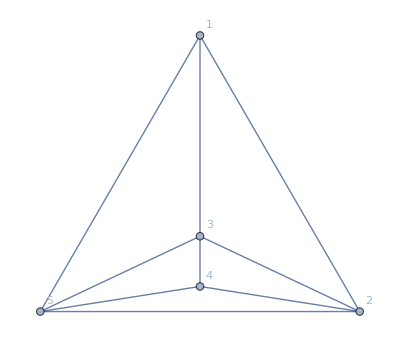
-Graphics-
{}→v14x2x3x5+v1x2x3x4x5
{1}→v2x3x4x5 (-3+x)
{2}→v1x3x4x5 (-4+x)+v14x3x5 (-3+x)
{3}→v1x2x4x5 (-4+x)+v14x2x5 (-3+x)
{5}→v1x2x3x4 (-4+x)+v14x2x3 (-3+x)
{4}→v1x2x3x5 (-3+x)
{1,2}→v3x4x5 (-3+x)^2
{1,3}→v2x4x5 (-3+x)^2
{1,5}→v2x3x4 (-3+x)^2
{1,4}→v2x3x5 (-3+x)^2
{2,3}→v1x4x5 (-4+x) (-3+x)+v14x5 (-3+x) (-2+x)
{2,5}→v1x3x4 (-4+x) (-3+x)+v14x3 (-3+x) (-2+x)
{2,4}→v1x3x5 (-3+x)^2
{3,5}→v1x2x4 (-4+x) (-3+x)+v14x2 (-3+x) (-2+x)
{3,4}→v1x2x5 (-3+x)^2
{5,4}→v1x2x3 (-3+x)^2
{1,2,3}→v4x5 (-3+x)^2 (-2+x)
{1,2,5}→v3x4 (-3+x)^2 (-2+x)
{1,2,4}→v3x5 (-3+x)^2 (-2+x)
{1,3,5}→v2x4 (-3+x)^2 (-2+x)
{1,3,4}→v2x5 (-3+x)^2 (-2+x)
{1,5,4}→v2x3 (-3+x)^2 (-2+x)
{2,3,5}→v1x4 (-4+x) (-3+x) (-2+x)+v14 (-3+x) (-2+x) (-1+x)
{2,3,4}→v1x5 (-3+x)^2 (-2+x)
{2,5,4}→v1x3 (-3+x)^2 (-2+x)
{3,5,4}→v1x2 (-3+x)^2 (-2+x)
{1,2,3,5}→v4 (-3+x)^2 (-2+x) (-1+x)
{1,2,3,4}→v5 (-3+x)^2 (-2+x) (-1+x)
{1,2,5,4}→v3 (-3+x)^2 (-2+x) (-1+x)
{1,3,5,4}→v2 (-3+x)^2 (-2+x) (-1+x)
{2,3,5,4}→v1 (-3+x)^2 (-2+x) (-1+x)
{1,2,3,5,4}→(-3+x)^2 (-2+x) (-1+x) x

```mathematica
With[{g=ReadGrof [2]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
TableForm[
Monitor[
Table[s->MyRewrite[CalculateInOutFormula[g,s]],{s,Subsets[VertexList[g]]}],
s]
]
}
]
]
```

```mathematica
MyRewrite[6 v14x5+12 v1x4x5-5 v14x5 x-7 v1x4x5 x+v14x5 x^2+v1x4x5 x^2]
```

v1x4x5 (-4+x) (-3+x)+v14x5 (-3+x) (-2+x)

```mathematica
CoefficientList[6 v14x5+12 v1x4x5-5 v14x5 x-7 v1x4x5 x+v14x5 x^2+v1x4x5 x^2,v14x5]
```

{12 v1x4x5-7 v1x4x5 x+v1x4x5 x^2,6-5 x+x^2}

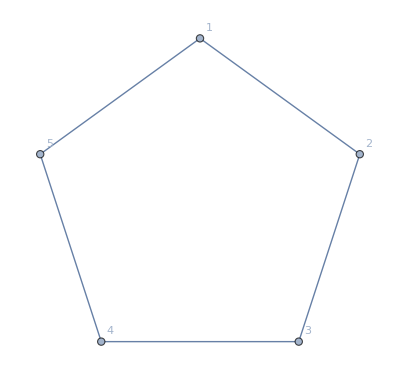
-Graphics-
{}→v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5
{1}→v24x35 (-2+x)+v24x3x5 (-2+x)+v2x35x4 (-2+x)+v2x3x4x5 (-2+x)+v25x3x4 (-1+x)
{2}→v14x35 (-2+x)+v14x3x5 (-2+x)+v1x35x4 (-2+x)+v1x3x4x5 (-2+x)+v13x4x5 (-1+x)
{3}→v14x25 (-2+x)+v14x2x5 (-2+x)+v1x25x4 (-2+x)+v1x2x4x5 (-2+x)+v1x24x5 (-1+x)
{4}→v13x25 (-2+x)+v13x2x5 (-2+x)+v1x25x3 (-2+x)+v1x2x3x5 (-2+x)+v1x2x35 (-1+x)
{5}→v13x24 (-2+x)+v13x2x4 (-2+x)+v1x24x3 (-2+x)+v1x2x3x4 (-2+x)+v14x2x3 (-1+x)
{1,2}→v35x4 (-2+x) (-1+x)+v3x4x5 (3-3 x+x^2)
{1,3}→v2x4x5 (-2+x)^2+v24x5 (-2+x) (-1+x)+v25x4 (-2+x) (-1+x)
{1,4}→v2x3x5 (-2+x)^2+v25x3 (-2+x) (-1+x)+v2x35 (-2+x) (-1+x)
{1,5}→v24x3 (-2+x) (-1+x)+v2x3x4 (3-3 x+x^2)
{2,3}→v14x5 (-2+x) (-1+x)+v1x4x5 (3-3 x+x^2)
{2,4}→v1x3x5 (-2+x)^2+v13x5 (-2+x) (-1+x)+v1x35 (-2+x) (-1+x)
{2,5}→v1x3x4 (-2+x)^2+v13x4 (-2+x) (-1+x)+v14x3 (-2+x) (-1+x)
{3,4}→v1x25 (-2+x) (-1+x)+v1x2x5 (3-3 x+x^2)
{3,5}→v1x2x4 (-2+x)^2+v14x2 (-2+x) (-1+x)+v1x24 (-2+x) (-1+x)
{4,5}→v13x2 (-2+x) (-1+x)+v1x2x3 (3-3 x+x^2)
{1,2,3}→v4x5 (-2+x) (2-2 x+x^2)
{1,2,4}→v35 (-2+x) (-1+x)^2+v3x5 (-2+x) (3-3 x+x^2)
{1,2,5}→v3x4 (-2+x) (2-2 x+x^2)
{1,3,4}→v25 (-2+x) (-1+x)^2+v2x5 (-2+x) (3-3 x+x^2)
{1,3,5}→v24 (-2+x) (-1+x)^2+v2x4 (-2+x) (3-3 x+x^2)
{1,4,5}→v2x3 (-2+x) (2-2 x+x^2)
{2,3,4}→v1x5 (-2+x) (2-2 x+x^2)
{2,3,5}→v14 (-2+x) (-1+x)^2+v1x4 (-2+x) (3-3 x+x^2)
{2,4,5}→v13 (-2+x) (-1+x)^2+v1x3 (-2+x) (3-3 x+x^2)
{3,4,5}→v1x2 (-2+x) (2-2 x+x^2)
{1,2,3,4}→v5 (-2+x) (-1+x) (2-2 x+x^2)
{1,2,3,5}→v4 (-2+x) (-1+x) (2-2 x+x^2)
{1,2,4,5}→v3 (-2+x) (-1+x) (2-2 x+x^2)
{1,3,4,5}→v2 (-2+x) (-1+x) (2-2 x+x^2)
{2,3,4,5}→v1 (-2+x) (-1+x) (2-2 x+x^2)
{1,2,3,4,5}→(-2+x) (-1+x) x (2-2 x+x^2)

```mathematica
With[{g=CycleGraph[5]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
TableForm[
Monitor[
Table[s->MyRewrite[CalculateInOutFormula[g,s]],{s,Subsets[VertexList[g]]}],
s]
]
}
]
]
```

```mathematica
MyRewrite2[form_,length_]:=Block[{vars=DeleteCases[DeleteDuplicates[ListofVars[form]],x]},
If[vars=={},
Style[PadRight[MatrixForm[CompleteBaseCoeff[form]],length],Italic],
Total[
Table[
v*Style[MatrixForm[PadRight[CompleteBaseCoeff[Last[CoefficientList[form,v]]],length]],Italic],
{v,vars}
]
]
]
]
```

```mathematica
CompleteBaseCoeff[3-3 x+x^2,Italic,Italic]
```

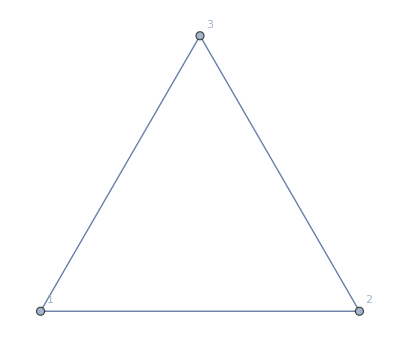
-Graphics-
{}→v1x2x3 (1)
{1}→v2x3 (-2
1)
{2}→v1x3 (-2
1)
{3}→v1x2 (-2
1)
{1,2}→v3 (2
-2
1)
{1,3}→v2 (2
-2
1)
{2,3}→v1 (2
-2
1)
{1,2,3}→(0
0
0
1)

```mathematica
With[{g=CycleGraph[3]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
TableForm[
Monitor[
Table[s->MyRewrite2[CalculateInOutFormula[g,s]],{s,Subsets[VertexList[g]]}],
s]
]
}
]
]
```

```mathematica
With[{g=CycleGraph[5]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
TableForm[
Monitor[
Table[s->MyRewrite2[CalculateInOutFormula[g,s],5],{s,Subsets[VertexList[g]]}],
s]
]
}
]
]
```

-Graphics-
{}→v13x24x5 (1
0
0
0
0)+v13x25x4 (1
0
0
0
0)+v13x2x4x5 (1
0
0
0
0)+v14x25x3 (1
0
0
0
0)+v14x2x35 (1
0
0
0
0)+v14x2x3x5 (1
0
0
0
0)+v1x24x35 (1
0
0
0
0)+v1x24x3x5 (1
0
0
0
0)+v1x25x3x4 (1
0
0
0
0)+v1x2x35x4 (1
0
0
0
0)+v1x2x3x4x5 (1
0
0
0
0)
{1}→v24x35 (-2
1
0
0
0)+v24x3x5 (-2
1
0
0
0)+v2x35x4 (-2
1
0
0
0)+v2x3x4x5 (-2
1
0
0
0)+v25x3x4 (-1
1
0
0
0)
{2}→v14x35 (-2
1
0
0
0)+v14x3x5 (-2
1
0
0
0)+v1x35x4 (-2
1
0
0
0)+v1x3x4x5 (-2
1
0
0
0)+v13x4x5 (-1
1
0
0
0)
{3}→v14x25 (-2
1
0
0
0)+v14x2x5 (-2
1
0
0
0)+v1x25x4 (-2
1
0
0
0)+v1x2x4x5 (-2
1
0
0
0)+v1x24x5 (-1
1
0
0
0)
{4}→v13x25 (-2
1
0
0
0)+v13x2x5 (-2
1
0
0
0)+v1x25x3 (-2
1
0
0
0)+v1x2x3x5 (-2
1
0
0
0)+v1x2x35 (-1
1
0
0
0)
{5}→v13x24 (-2
1
0
0
0)+v13x2x4 (-2
1
0
0
0)+v1x24x3 (-2
1
0
0
0)+v1x2x3x4 (-2
1
0
0
0)+v14x2x3 (-1
1
0
0
0)
{1,2}→v35x4 (2
-2
1
0
0)+v3x4x5 (3
-2
1
0
0)
{1,3}→v24x5 (2
-2
1
0
0)+v25x4 (2
-2
1
0
0)+v2x4x5 (4
-3
1
0
0)
{1,4}→v25x3 (2
-2
1
0
0)+v2x35 (2
-2
1
0
0)+v2x3x5 (4
-3
1
0
0)
{1,5}→v24x3 (2
-2
1
0
0)+v2x3x4 (3
-2
1
0
0)
{2,3}→v14x5 (2
-2
1
0
0)+v1x4x5 (3
-2
1
0
0)
{2,4}→v13x5 (2
-2
1
0
0)+v1x35 (2
-2
1
0
0)+v1x3x5 (4
-3
1
0
0)
{2,5}→v13x4 (2
-2
1
0
0)+v14x3 (2
-2
1
0
0)+v1x3x4 (4
-3
1
0
0)
{3,4}→v1x25 (2
-2
1
0
0)+v1x2x5 (3
-2
1
0
0)
{3,5}→v14x2 (2
-2
1
0
0)+v1x24 (2
-2
1
0
0)+v1x2x4 (4
-3
1
0
0)
{4,5}→v13x2 (2
-2
1
0
0)+v1x2x3 (3
-2
1
0
0)
{1,2,3}→v4x5 (-4
3
-1
1
0)
{1,2,4}→v3x5 (-6
5
-2
1
0)+v35 (-2
2
-1
1
0)
{1,2,5}→v3x4 (-4
3
-1
1
0)
{1,3,4}→v2x5 (-6
5
-2
1
0)+v25 (-2
2
-1
1
0)
{1,3,5}→v2x4 (-6
5
-2
1
0)+v24 (-2
2
-1
1
0)
{1,4,5}→v2x3 (-4
3
-1
1
0)
{2,3,4}→v1x5 (-4
3
-1
1
0)
{2,3,5}→v1x4 (-6
5
-2
1
0)+v14 (-2
2
-1
1
0)
{2,4,5}→v1x3 (-6
5
-2
1
0)+v13 (-2
2
-1
1
0)
{3,4,5}→v1x2 (-4
3
-1
1
0)
{1,2,3,4}→v5 (4
-4
2
1
1)
{1,2,3,5}→v4 (4
-4
2
1
1)
{1,2,4,5}→v3 (4
-4
2
1
1)
{1,3,4,5}→v2 (4
-4
2
1
1)
{2,3,4,5}→v1 (4
-4
2
1
1)
{1,2,3,4,5}→(0
0
0
5
5
1)

```mathematica
CalculateInOutFormulaFull[g_,in_,out_]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex},
edges=EdgeList[g];
For[pos=1,pos <=Length[edges],pos++,
currentEdge=edges[[pos]];
isInOut=MemberQ[in,currentEdge[[1]]]&&MemberQ[out,currentEdge[[2]]];
If[!isInOut,
isInOut=MemberQ[in,currentEdge[[2]]]&&MemberQ[out,currentEdge[[1]]];
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
If[isInOut,
gContract=GContract[g,currentEdge];
repVertex={currentEdge[[1]]->currentEdge[[2]]};
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
gRemove=EdgeDelete[g,currentEdge];
resContract=CalculateInOutFormulaFull[gContract,DeleteCases[in,currentEdge[[1]]],out];
resRemove=CalculateInOutFormulaFull[gRemove,in,out];
(*Print[currentEdge->{Graph[gRemove,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resRemove,Graph[gContract,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resContract}];*)
result=resRemove-resContract;
Return[result]
];
];
gIn=Subgraph[g,in];
gOut=Subgraph[g,out];
resIn=If[VertexCount[gIn]==0,1,Fold [Plus,Map[SetsToSymbol[SymbolToSets[#],"i"]&,FindFullFormula[gIn]]]];
resOut=If[VertexCount[gOut]==0,1,Fold [Plus,FindFullFormula[gOut]]];
(*Print[{Graph[gIn,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resIn,Graph[gOut,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"], resOut,resIn*resOut}];*)
Return[resIn*resOut]
]
```

```mathematica
CalculateInOutFormulaFull[g_,in_]:=CalculateInOutFormulaFull[g,in,Select[VertexList[g],!MemberQ[in,#]&]]
```

```mathematica
MyRewrite4[form_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],"v"]&]},
If[vars=={},
Factor[form],
Total[
Table[
v*Factor[Last[CoefficientList[form,v]]],
{v,vars}
]
]
]
]
```

```mathematica
With[{g=ReadGrof[2]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
TableForm[
Monitor[
Table[s->MyRewrite4[CalculateInOutFormulaFull[g,s]],{s,Subsets[VertexList[g]]}],
s]
]
}
]
]
```

-Graphics-
{}→v14x2x3x5+v1x2x3x4x5
{1}→(-3+i1) v2x3x4x5
{2}→(-3+i2) v14x3x5+(-4+i2) v1x3x4x5
{3}→(-3+i3) v14x2x5+(-4+i3) v1x2x4x5
{5}→(-3+i5) v14x2x3+(-4+i5) v1x2x3x4
{4}→(-3+i4) v1x2x3x5
{1,2}→(9-3 i1+i1x2-2 i2) v3x4x5
{1,3}→(9-3 i1+i1x3-2 i3) v2x4x5
{1,5}→(9-3 i1+i1x5-2 i5) v2x3x4
{1,4}→(9-3 i1+i14+i1x4-3 i4) v2x3x5
{2,3}→(6-2 i2+i2x3-2 i3) v14x5+(12-3 i2+i2x3-3 i3) v1x4x5
{2,5}→(6-2 i2+i2x5-2 i5) v14x3+(12-3 i2+i2x5-3 i5) v1x3x4
{2,4}→(9-2 i2+i2x4-3 i4) v1x3x5
{3,5}→(6-2 i3+i3x5-2 i5) v14x2+(12-3 i3+i3x5-3 i5) v1x2x4
{3,4}→(9-2 i3+i3x4-3 i4) v1x2x5
{5,4}→(9-3 i4+i4x5-2 i5) v1x2x3
{1,2,3}→(-18+6 i1-2 i1x2+i1x2x3-2 i1x3+4 i2-i2x3+4 i3) v4x5
{1,2,5}→(-18+6 i1-2 i1x2+i1x2x5-2 i1x5+4 i2-i2x5+4 i5) v3x4
{1,2,4}→(-18+6 i1-2 i14+i14x2-2 i1x2+i1x2x4-2 i1x4+4 i2-2 i2x4+6 i4) v3x5
{1,3,5}→(-18+6 i1-2 i1x3+i1x3x5-2 i1x5+4 i3-i3x5+4 i5) v2x4
{1,3,4}→(-18+6 i1-2 i14+i14x3-2 i1x3+i1x3x4-2 i1x4+4 i3-2 i3x4+6 i4) v2x5
{1,5,4}→(-18+6 i1-2 i14+i14x5-2 i1x4+i1x4x5-2 i1x5+6 i4-2 i4x5+4 i5) v2x3
{2,3,5}→(-6+2 i2-i2x3+i2x3x5-i2x5+2 i3-i3x5+2 i5) v14+(-24+6 i2-2 i2x3+i2x3x5-2 i2x5+6 i3-2 i3x5+6 i5) v1x4
{2,3,4}→(-18+4 i2-i2x3+i2x3x4-2 i2x4+4 i3-2 i3x4+6 i4) v1x5
{2,5,4}→(-18+4 i2-2 i2x4+i2x4x5-i2x5+6 i4-2 i4x5+4 i5) v1x3
{3,5,4}→(-18+4 i3-2 i3x4+i3x4x5-i3x5+6 i4-2 i4x5+4 i5) v1x2
{1,2,3,5}→(18-6 i1+2 i1x2-i1x2x3+i1x2x3x5-i1x2x5+2 i1x3-i1x3x5+2 i1x5-4 i2+i2x3+i2x5-4 i3+i3x5-4 i5) v4
{1,2,3,4}→(18-6 i1+2 i14-i14x2+i14x2x3-i14x3+2 i1x2-i1x2x3+i1x2x3x4-i1x2x4+2 i1x3-i1x3x4+2 i1x4-4 i2+i2x3-i2x3x4+2 i2x4-4 i3+2 i3x4-6 i4) v5
{1,2,5,4}→(18-6 i1+2 i14-i14x2+i14x2x5-i14x5+2 i1x2-i1x2x4+i1x2x4x5-i1x2x5+2 i1x4-i1x4x5+2 i1x5-4 i2+2 i2x4-i2x4x5+i2x5-6 i4+2 i4x5-4 i5) v3
{1,3,5,4}→(18-6 i1+2 i14-i14x3+i14x3x5-i14x5+2 i1x3-i1x3x4+i1x3x4x5-i1x3x5+2 i1x4-i1x4x5+2 i1x5-4 i3+2 i3x4-i3x4x5+i3x5-6 i4+2 i4x5-4 i5) v2
{2,3,5,4}→(18-4 i2+i2x3-i2x3x4+i2x3x4x5+2 i2x4-i2x4x5+i2x5-4 i3+2 i3x4-i3x4x5+i3x5-6 i4+2 i4x5-4 i5) v1
{1,2,3,5,4}→i14x2x3x5+i1x2x3x4x5

```mathematica
ChromaticPolynomial[Graph[{},{}],x]
```

1

```mathematica
Map[SetsToSymbol[SymbolToSets[#],"v"]&,ListofVars[+6 i1-2 i1x2+i1x2x3-2 i1x3+4 i2-i2x3+4 i3]]//Length
```

7

```mathematica
Map[SetsToSymbol[SymbolToSets[#],"v"]&,ListofVars[(18-4 i2+i2x3-i2x3x4+i2x3x4x5+2 i2x4-i2x4x5+i2x5-4 i3+2 i3x4-i3x4x5+i3x5-6 i4+2 i4x5-4 i5)]]//Length
```

14

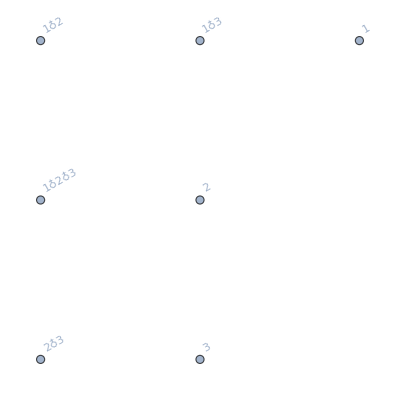

```mathematica
FormulaGraphReverse[Map[SetsToSymbol[SymbolToSets[#],"v"]&,ListofVars[+6 i1-2 i1x2+i1x2x3-2 i1x3+4 i2-i2x3+4 i3]]]
```